```mathematica
FileNames["/home/carla/GDC/MUR/*.txt"]
```

{/home/carla/GDC/MUR/MUR_DOJ.txt,/home/carla/GDC/MUR/MUR_F.txt,/home/carla/GDC/MUR/MUR_Z.txt}

```mathematica
{"/home/carla/GDC/MUR/MUR_Z.txt","/home/carla/GDC/MUR/MUR_F.txt","/home/carla/GDC/MUR/MUR_Z.txt"}
```

{/home/carla/GDC/MUR/MUR_Z.txt,/home/carla/GDC/MUR/MUR_F.txt,/home/carla/GDC/MUR/MUR_Z.txt}

```mathematica
dataDLB=Map[Get[#]&, FileNames["/home/carla/GDC/DLB/*.txt"]][[3]]
dataMUR=Map[Get[#]&, FileNames["/home/carla/GDC/MUR/*.txt"]][[3]];
dataLYE=Map[Get[#]&, FileNames["/home/carla/GDC/LYE/*.txt"]][[3]];
dataPHI=Map[Get[#]&, FileNames["/home/carla/GDC/PHI/*.txt"]][[3]];
dataSED=Map[Get[#]&, FileNames["/home/carla/GDC/SED/*.txt"]][[3]];
dataAUS=Map[Get[#]&, FileNames["/home/carla/GDC/AUS/*.txt"]][[3]];
```

{{0,1.},{0.5,1.},{1,1.},{1.5,1.},{2,0.000635999},{2.5,0.000642717},{3,0.00597582},{3.5,0.00596861},{4,0.00693882},{4.5,0.00397728},{5,0.00385126},{5.5,0.000814793},{6,0.0222066},{8,1}}

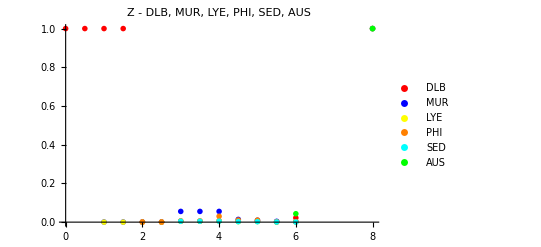

```mathematica
plotDMLPSA=ListPlot[{dataDLB,dataMUR, dataLYE, dataPHI, dataSED, dataAUS},PlotLegends->{"DLB","MUR","LYE", "PHI", "SED", "AUS"},PlotStyle->{Red,Blue,Yellow, Orange, Cyan, Green},PlotRange->All,PlotLabel->"Z - DLB, MUR, LYE, PHI, SED, AUS",PlotMarkers->{{"D",12},{"M",12},{"L",12}, {"P",12},{"S",12},{"A",12}}]
```

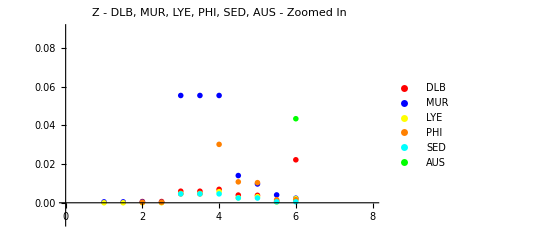

```mathematica
plotDMLPSAZoomedIn=ListPlot[{dataDLB,dataMUR, dataLYE, dataPHI, dataSED, dataAUS},PlotLegends->{"DLB","MUR","LYE", "PHI", "SED", "AUS"},PlotStyle->{Red,Blue,Yellow, Orange, Cyan, Green},PlotRange->{-0.01,0.09},PlotLabel->"Z - DLB, MUR, LYE, PHI, SED, AUS - Zoomed In",PlotMarkers->{{"D",12},{"M",12},{"L",12}, {"P",12},{"S",12},{"A",12}}]
```

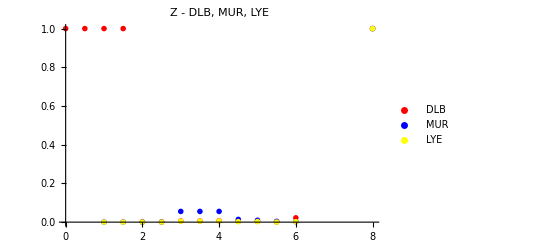

```mathematica
plotDML=ListPlot[{dataDLB,dataMUR, dataLYE},PlotLegends->{"DLB","MUR","LYE"},PlotStyle->{Red,Blue,Yellow},PlotRange->All,PlotLabel->"Z - DLB, MUR, LYE",PlotMarkers->{{"D",12},{"M",12},{"L",12}}]
```

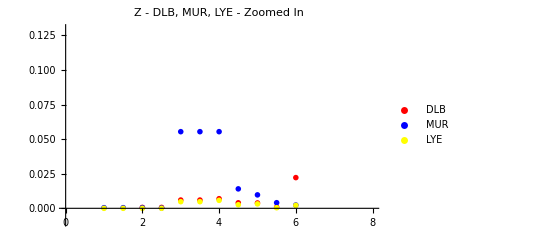

```mathematica
plotDMLZoomedIn=ListPlot[{dataDLB,dataMUR, dataLYE},PlotLegends->{"DLB","MUR","LYE"},PlotStyle->{Red,Blue,Yellow},PlotRange->{-0.01,0.13},PlotLabel->"Z - DLB, MUR, LYE - Zoomed In",PlotMarkers->{{"D",12},{"M",12},{"L",12}}]
```

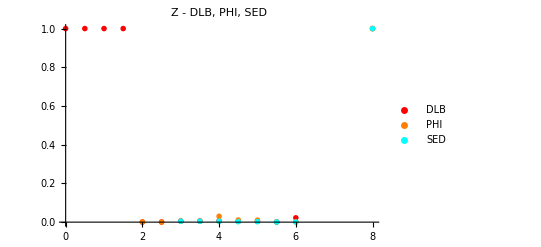

```mathematica
plotDPS=ListPlot[{dataDLB, dataPHI, dataSED},PlotLegends->{"DLB","PHI", "SED"},PlotStyle->{Red,Orange,Cyan},PlotRange->All,PlotLabel->"Z - DLB, PHI, SED",PlotMarkers->{{"D",12},{"P",12},{"S",12}}]
```

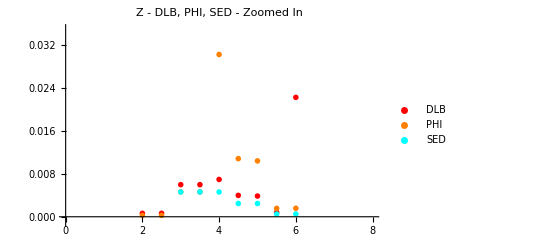

```mathematica
plotDPSZoomedIn=ListPlot[{dataDLB, dataPHI, dataSED},PlotLegends->{"DLB","PHI", "SED"},PlotStyle->{Red,Orange,Cyan},PlotRange->{-0.001,0.035},PlotLabel->"Z - DLB, PHI, SED - Zoomed In",PlotMarkers->{{"D",12},{"P",12},{"S",12}}]
```

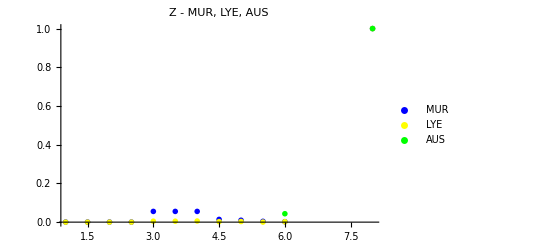

```mathematica
plotMLA=ListPlot[{dataMUR, dataLYE, dataAUS},PlotLegends->{"MUR","LYE", "AUS"},PlotStyle->{Blue,Yellow, Green},PlotRange->All,PlotLabel->"Z - MUR, LYE, AUS",PlotMarkers->{{"M",12},{"L",12},{"A",12}}]
```

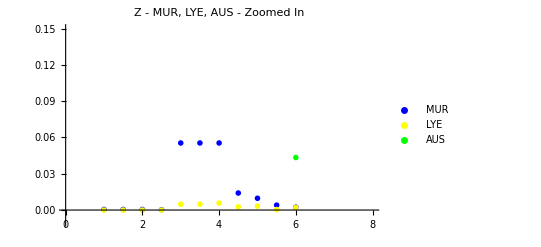

```mathematica
plotMLAZoomedIn=ListPlot[{dataMUR, dataLYE, dataAUS},PlotLegends->{"MUR","LYE", "AUS"},PlotStyle->{Blue,Yellow, Green},PlotRange->{-0.01,0.15},PlotLabel->"Z - MUR, LYE, AUS - Zoomed In",PlotMarkers->{{"M",12},{"L",12},{"A",12}}]
```

```mathematica
SetDirectory["/home/carla/GDC/ALL_PERS/Z"];
Put[<|"DLB"->dataDLB,"MUR"->dataMUR,"LYE"->dataLYE, "PHI"->dataPHI,"SED"->dataSED,"AUS"->dataAUS|>,"Z.txt"]
Export["Z_DMLPSA.jpeg",plotDMLPSA,ImageSize->850]
Export["Z_DMLPSA_ZoomedIn.jpeg",plotDMLPSAZoomedIn,ImageSize->850]
Export["Z_DML.jpeg",plotDML,ImageSize->850]
Export["Z_DML_ZoomedIn.jpeg",plotDMLZoomedIn,ImageSize->850]
Export["Z_DPS.jpeg",plotDPS,ImageSize->850]
Export["Z_DPS_ZoomedIn.jpeg",plotDPSZoomedIn,ImageSize->850]
Export["Z_MLA.jpeg",plotMLA,ImageSize->850]
Export["Z_MLA_ZoomedIn.jpeg",plotMLAZoomedIn,ImageSize->850]
```

Z_DMLPSA.jpeg

Z_DMLPSA_ZoomedIn.jpeg

Z_DML.jpeg

Z_DML_ZoomedIn.jpeg

Z_DPS.jpeg

Z_DPS_ZoomedIn.jpeg

Z_MLA.jpeg

Z_MLA_ZoomedIn.jpeg

```mathematica
"Z_DMLPSA.jpeg"
```

Z_DMLPSA.jpeg

```mathematica
"Z_DMLPSA_ZoomedIn.jpeg"
```

Z_DMLPSA_ZoomedIn.jpeg

```mathematica
"Z_DML.jpeg"
```

Z_DML.jpeg

```mathematica
"Z_DML_ZoomedIn.jpeg"
```

Z_DML_ZoomedIn.jpeg

```mathematica
"Z_DPS.jpeg"
```

Z_DPS.jpeg

```mathematica
"Z_DPS_ZoomedIn.jpeg"
```

Z_DPS_ZoomedIn.jpeg

```mathematica
"Z_MLA.jpeg"
```

Z_MLA.jpeg

```mathematica
"Z_MLA_ZoomedIn.jpeg"
```

Z_MLA_ZoomedIn.jpeg